```mathematica
ClearAll["Global`*"]
```

```mathematica
axiom1={ForAll[{a},GCD[a,a]==a]}
axiom2={ForAll[{a,b},GCD[a,b]==GCD[b,a]]}
axiom3={ForAll[{a,b,c},GCD[a,gcd[b,c]]==GCD[gcd[a,b],c]]}
hyp1={d==GCD[a,b]}
hyp2={GCD[a,t]==t}
hyp3={GCD[b,t]==t}
axioms=Union[axiom1,axiom2,axiom3]
hypotheses=Union[hyp1,hyp2,hyp3]
FindEquationalProof[GCD[d,t]==t,Union[axioms,hypotheses]]
```

{∀_{a}GCD[a,a]==a}

{True}

{∀_{a,b,c}GCD[a,gcd[b,c]]==GCD[c,gcd[a,b]]}

{d==GCD[a,b]}

{GCD[a,t]==t}

{GCD[b,t]==t}

{True,∀_{a}GCD[a,a]==a,∀_{a,b,c}GCD[a,gcd[b,c]]==GCD[c,gcd[a,b]]}

{d==GCD[a,b],GCD[a,t]==t,GCD[b,t]==t}

Failure[…]

```mathematica
axiom1={ForAll[{a},gccd[a,a]==a]}
axiom2={ForAll[{a,b},gccd[a,b]==gccd[b,a]]}
axiom3={ForAll[{a,b,c},gccd[a,gccd[b,c]]==gccd[gccd[a,b],c]]}
hyp1={d==gccd[a,b]}
hyp2={gccd[a,t]==t}
hyp3={gccd[b,t]==t}
axioms=Union[axiom1,axiom2,axiom3]
hypotheses=Union[hyp1,hyp2,hyp3]
proof=FindEquationalProof[gccd[d,t]==t,Union[axioms,hypotheses]]
```

{∀_{a}gccd[a,a]==a}

{∀_{a,b}gccd[a,b]==gccd[b,a]}

{∀_{a,b,c}gccd[a,gccd[b,c]]==gccd[gccd[a,b],c]}

{d==gccd[a,b]}

{gccd[a,t]==t}

{gccd[b,t]==t}

{∀_{a}gccd[a,a]==a,∀_{a,b}gccd[a,b]==gccd[b,a],∀_{a,b,c}gccd[a,gccd[b,c]]==gccd[gccd[a,b],c]}

{d==gccd[a,b],gccd[a,t]==t,gccd[b,t]==t}

ProofObject[…]

```mathematica
proof["ProofDataset"]
```

```mathematica
axiom1={ForAll[{a},gccd[a,a]==a]}
axiom2={ForAll[{a,b},gccd[a,b]==gccd[b,a]]}
axiom3={ForAll[{a,b,c},gccd[a,gccd[b,c]]==gccd[gccd[a,b],c]]}
hyp1={d==gccd[a,b]}
hyp2={gccd[a,t]==t}
hyp3={gccd[b,t]==t}
axioms=Union[axiom1,axiom2,axiom3]
hypotheses=Union[hyp1,hyp2,hyp3]
proof=FindEquationalProof[gccd[d,t]==t,Union[axioms,hypotheses]]
```

```mathematica
axiomPythagoras = {ForAll[{hyp,opp,adj},hyp^2==opp^2+adj^2]}
axiomSin = {ForAll[{a},sin[a]==opp/hyp]}
axiomSin2= {ForAll[{a},sin[a]^2==opp^2/hyp^2]}
axiomCos = {ForAll[{a},cos[a]==adj/hyp]}
axiomCos2 = {ForAll[{a},cos[a]^2==adj^2/hyp^2]}
axiomX = {ForAll[{alpha,a},alpha==cos[a]]}
axiomY = {ForAll[{beta,a},beta==sin[a]]}
axiomss=Union[axiomPythagoras,axiomSin,axiomCos,axiomSin2,axiomCos2]

proof2=FindEquationalProof[sin[a]^2+cos[a]^2==1,axiomss]
```

{∀_{hyp,opp,adj}hyp^2==adj^2+opp^2}

{∀_{a}sin[a]==opp/hyp}

{∀_{a}sin[a]^2==opp^2/hyp^2}

{∀_{a}cos[a]==adj/hyp}

{∀_{a}cos[a]^2==adj^2/hyp^2}

{∀_{alpha,a}alpha==cos[a]}

{∀_{beta,a}beta==sin[a]}

{∀_{a}cos[a]==adj/hyp,∀_{a}cos[a]^2==adj^2/hyp^2,∀_{a}sin[a]==opp/hyp,∀_{a}sin[a]^2==opp^2/hyp^2,∀_{hyp,opp,adj}hyp^2==adj^2+opp^2}

Failure[…]

```mathematica
proof2["ProofNotebook"]
```

Axiom 1
We are given that:
x1==sin[x2]
Hypothesis 1
We would like to show that:
cos[c]^2+sin[c]^2==1
Substitution Lemma 1
It can be shown that:
cos[c]^2+sin[c]^2==sin[1]
Proof
We start by taking Hypothesis 1, and apply the substitution:
x1_→sin[1]
which follows from Axiom 1.
Conclusion 1
We obtain the conclusion:
True
Proof
Take Substitution Lemma 1, and apply the substitution:
x1_→sin[1]
which follows from Axiom 1.

```mathematica
proof["ProofNotebook"]
```

Axiom 1
We are given that:
x1==gccd[x1,x1]
Axiom 2
We are given that:
gccd[x1,x2]==gccd[x2,x1]
Axiom 3
We are given that:
gccd[x1,gccd[x2,x3]]==gccd[gccd[x1,x2],x3]
Axiom 4
We are given that:
gccd[a,t]==t
Axiom 5
We are given that:
gccd[a,b]==d
Axiom 6
We are given that:
gccd[b,t]==t
Hypothesis 1
We would like to show that:
gccd[d,t]==t
Substitution Lemma 1
It can be shown that:
gccd[b,a]==d
Proof
We start by taking Axiom 5, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Substitution Lemma 2
It can be shown that:
gccd[t,d]==t
Proof
We start by taking Hypothesis 1, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Substitution Lemma 3
It can be shown that:
gccd[gccd[a,t],d]==t
Proof
We start by taking Substitution Lemma 2, and apply the substitution:
t→gccd[a,t]
which follows from Axiom 4.
Substitution Lemma 4
It can be shown that:
gccd[gccd[t,a],d]==t
Proof
We start by taking Substitution Lemma 3, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Substitution Lemma 5
It can be shown that:
gccd[t,gccd[a,d]]==t
Proof
We start by taking Substitution Lemma 4, and apply the substitution:
gccd[gccd[x1_,x2_],x3_]→gccd[x1,gccd[x2,x3]]
which follows from Axiom 3.
Substitution Lemma 6
It can be shown that:
gccd[t,gccd[d,a]]==t
Proof
We start by taking Substitution Lemma 5, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Substitution Lemma 7
It can be shown that:
gccd[gccd[d,a],t]==t
Proof
We start by taking Substitution Lemma 6, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Substitution Lemma 8
It can be shown that:
gccd[gccd[gccd[b,a],a],t]==t
Proof
We start by taking Substitution Lemma 7, and apply the substitution:
d→gccd[b,a]
which follows from Substitution Lemma 1.
Substitution Lemma 9
It can be shown that:
gccd[gccd[b,gccd[a,a]],t]==t
Proof
We start by taking Substitution Lemma 8, and apply the substitution:
gccd[gccd[x1_,x2_],x3_]→gccd[x1,gccd[x2,x3]]
which follows from Axiom 3.
Substitution Lemma 10
It can be shown that:
gccd[b,gccd[gccd[a,a],t]]==t
Proof
We start by taking Substitution Lemma 9, and apply the substitution:
gccd[gccd[x1_,x2_],x3_]→gccd[x1,gccd[x2,x3]]
which follows from Axiom 3.
Substitution Lemma 11
It can be shown that:
gccd[gccd[gccd[a,a],t],b]==t
Proof
We start by taking Substitution Lemma 10, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Substitution Lemma 12
It can be shown that:
gccd[gccd[a,t],b]==t
Proof
We start by taking Substitution Lemma 11, and apply the substitution:
gccd[x1_,x1_]→x1
which follows from Axiom 1.
Substitution Lemma 13
It can be shown that:
gccd[t,b]==t
Proof
We start by taking Substitution Lemma 12, and apply the substitution:
gccd[a,t]→t
which follows from Axiom 4.
Substitution Lemma 14
It can be shown that:
gccd[b,t]==t
Proof
We start by taking Substitution Lemma 13, and apply the substitution:
gccd[x1_,x2_]→gccd[x2,x1]
which follows from Axiom 2.
Conclusion 1
We obtain the conclusion:
True
Proof
Take Substitution Lemma 14, and apply the substitution:
t→gccd[b,t]
which follows from Axiom 6.

```mathematica
axiomDef1= {ForAll[{a},Implies[Element[a,A],]]}
```

```mathematica
axiomDef1= Implies[ForAll[{a},And[Element[a,A],Element[a,B]]],A ⊂B]
```

∀_{a}(a∈A&&a∈B)⇒A⊂B

```mathematica
Atom
```

```mathematica
Head@axiomDef1
```

Implies

```mathematica
Information[Implies]
```

```mathematica
(*
Boolean Algebra Axioms

*)
```

```mathematica
BooleanTable[{x,Not[x]},{x}]//Grid
```

True | False
False | True

```mathematica
negationP:={ForAll[{p},not[p]==Not[p]]}
commutativityAxiomAnd:= {ForAll[{p,q},and[p,q]==and[q,p]]}
commutativityAxiomOr:= {ForAll[{p,q},or[p,q]==or[q,p]]}
associativityAxiomAnd:={ForAll[{p,q,r},and[and[p,q],r]==and[p,and[q,r]]]}
associativityAxiomOr:= {ForAll[{p,q,r},or[or[p,q],r]==or[p,or[q,r]]]}
distributivityAxiomAnd:= {ForAll[{p,q,r},and[p,or[q,r]]==or[and[p,q],and[q,r]]]}
distributivityAxiomOr:= {ForAll[{p,q,r},or[p,and[q,r]]==and[or[p,q],or[p,r]]]}

identityAxiomAnd:={ForAll[{p},and[p,tau]==p]}
identityAxiomOr:={ForAll[{p},and[p,con]==con]}
negationAnd:={ForAll[{p},and[p,not[p]]==con]}
negationOr:={ForAll[{p},or[p,not[p]]==tau]}
```

```mathematica
booleanAlgebraAxioms= Union[negationP,commutativityAxiomAnd,commutativityAxiomOr,associativityAxiomAnd,associativityAxiomOr,distributivityAxiomAnd,distributivityAxiomOr,identityAxiomAnd,identityAxiomOr,negationAnd,negationOr]
```

{∀_{p}and[p,con]==con,∀_{p}and[p,tau]==p,∀_{p}and[p,not[p]]==con,∀_{p}not[p]==!p,∀_{p}or[p,not[p]]==tau,∀_{p,q}and[p,q]==and[q,p],∀_{p,q}or[p,q]==or[q,p],∀_{p,q,r}and[p,or[q,r]]==or[and[p,q],and[q,r]],∀_{p,q,r}and[and[p,q],r]==and[p,and[q,r]],∀_{p,q,r}or[p,and[q,r]]==and[or[p,q],or[p,r]],∀_{p,q,r}or[or[p,q],r]==or[p,or[q,r]]}

```mathematica
proofBoolean=FindEquationalProof[not[and[p,q]]==or[not[p],not[q]],booleanAlgebraAxioms]
```

ProofObject[…]

```mathematica
proofBoolean["ProofNotebook"]
```

Axiom 1
We are given that:
∀_{p}and[p,con]==con
Axiom 2
We are given that:
∀_{p}and[p,tau]==p
Axiom 3
We are given that:
∀_{p}and[p,not[p]]==con
Axiom 4
We are given that:
∀_{p}not[p]==!p
Axiom 5
We are given that:
∀_{p}or[p,not[p]]==tau
Axiom 6
We are given that:
∀_{p,q}and[p,q]==and[q,p]
Axiom 7
We are given that:
∀_{p,q}or[p,q]==or[q,p]
Axiom 8
We are given that:
∀_{p,q,r}and[p,or[q,r]]==or[and[p,q],and[q,r]]
Axiom 9
We are given that:
∀_{p,q,r}and[and[p,q],r]==and[p,and[q,r]]
Axiom 10
We are given that:
∀_{p,q,r}or[p,and[q,r]]==and[or[p,q],or[p,r]]
Axiom 11
We are given that:
∀_{p,q,r}or[or[p,q],r]==or[p,or[q,r]]
Hypothesis 1
We would like to show that:
not[and[p,q]]==or[not[p],not[q]]
Equationalized Axiom 1
We generate the ''equationalized'' axiom:
x1==and[x1,tau]
Equationalized Axiom 2
We generate the ''equationalized'' axiom:
and[x1,x2]==and[x2,x1]
Equationalized Axiom 3
We generate the ''equationalized'' axiom:
and[x1,or[x2,x3]]==or[and[x1,x2],and[x2,x3]]
Equationalized Axiom 4
We generate the ''equationalized'' axiom:
and[x1,con]==con
Equationalized Axiom 5
We generate the ''equationalized'' axiom:
and[x1,not[x1]]==con
Equationalized Axiom 6
We generate the ''equationalized'' axiom:
and[or[x1,x2],or[x1,x3]]==or[x1,and[x2,x3]]
Equationalized Axiom 7
We generate the ''equationalized'' axiom:
or[x1,x2]==or[x2,x1]
Equationalized Axiom 8
We generate the ''equationalized'' axiom:
or[x1,not[x1]]==tau
Equationalized Axiom 9
We generate the ''equationalized'' axiom:
not[x1]==!x1
Equationalized Hypothesis 1
We generate the ''equationalized'' hypothesis:
or[not[p],not[q]]==not[and[p,q]]
Critical Pair Lemma 1
The following expressions are equivalent:
and[tau,x1]==x1
Proof
Note that the input for the rule:
and[x1_,x2_]<->and[x2_,x1_]
contains a subpattern of the form:
and[x1_,x2_]
which can be unified with the input for the rule:
and[x1_,tau]→x1
where these rules follow from Equationalized Axiom 2 and Equationalized Axiom 1 respectively.
Critical Pair Lemma 2
The following expressions are equivalent:
and[x1,or[tau,x2]]==or[x1,and[tau,x2]]
Proof
Note that the input for the rule:
or[and[x1_,x2_],and[x2_,x3_]]→and[x1,or[x2,x3]]
contains a subpattern of the form:
and[x1_,x2_]
which can be unified with the input for the rule:
and[x1_,tau]→x1
where these rules follow from Equationalized Axiom 3 and Equationalized Axiom 1 respectively.
Critical Pair Lemma 3
The following expressions are equivalent:
con==and[con,x1]
Proof
Note that the input for the rule:
and[x1_,con]→con
contains a subpattern of the form:
and[x1_,con]
which can be unified with the input for the rule:
and[x1_,x2_]<->and[x2_,x1_]
where these rules follow from Equationalized Axiom 4 and Equationalized Axiom 2 respectively.
Substitution Lemma 1
It can be shown that:
or[x1,!x1]==tau
Proof
We start by taking Equationalized Axiom 8, and apply the substitution:
not[x1_]→!x1
which follows from Equationalized Axiom 9.
Substitution Lemma 2
It can be shown that:
and[x1,!x1]==con
Proof
We start by taking Equationalized Axiom 5, and apply the substitution:
not[x1_]→!x1
which follows from Equationalized Axiom 9.
Critical Pair Lemma 4
The following expressions are equivalent:
con==!tau
Proof
Note that the input for the rule:
and[x1_,!x1_]→con
contains a subpattern of the form:
and[x1_,!x1_]
which can be unified with the input for the rule:
and[tau,x1_]→x1
where these rules follow from Substitution Lemma 2 and Critical Pair Lemma 1 respectively.
Critical Pair Lemma 5
The following expressions are equivalent:
tau==or[tau,con]
Proof
Note that the input for the rule:
or[x1_,!x1_]→tau
contains a subpattern of the form:
!x1_
which can be unified with the input for the rule:
!tau→con
where these rules follow from Substitution Lemma 1 and Critical Pair Lemma 4 respectively.
Critical Pair Lemma 6
The following expressions are equivalent:
or[tau,and[con,x1]]==and[tau,or[tau,x1]]
Proof
Note that the input for the rule:
and[or[x1_,x2_],or[x1_,x3_]]→or[x1,and[x2,x3]]
contains a subpattern of the form:
or[x1_,x2_]
which can be unified with the input for the rule:
or[tau,con]→tau
where these rules follow from Equationalized Axiom 6 and Critical Pair Lemma 5 respectively.
Substitution Lemma 3
It can be shown that:
or[tau,con]==and[tau,or[tau,x1]]
Proof
We start by taking Critical Pair Lemma 6, and apply the substitution:
and[con,x1_]→con
which follows from Critical Pair Lemma 3.
Substitution Lemma 4
It can be shown that:
tau==and[tau,or[tau,x1]]
Proof
We start by taking Substitution Lemma 3, and apply the substitution:
or[tau,con]→tau
which follows from Critical Pair Lemma 5.
Substitution Lemma 5
It can be shown that:
tau==or[tau,x1]
Proof
We start by taking Substitution Lemma 4, and apply the substitution:
and[tau,x1_]→x1
which follows from Critical Pair Lemma 1.
Substitution Lemma 6
It can be shown that:
and[x1,tau]==or[x1,and[tau,x2]]
Proof
We start by taking Critical Pair Lemma 2, and apply the substitution:
or[tau,x1_]→tau
which follows from Substitution Lemma 5.
Substitution Lemma 7
It can be shown that:
x1==or[x1,and[tau,x2]]
Proof
We start by taking Substitution Lemma 6, and apply the substitution:
and[x1_,tau]→x1
which follows from Equationalized Axiom 1.
Substitution Lemma 8
It can be shown that:
x1==or[x1,x2]
Proof
We start by taking Substitution Lemma 7, and apply the substitution:
and[tau,x1_]→x1
which follows from Critical Pair Lemma 1.
Substitution Lemma 9
It can be shown that:
x1==or[x2,x1]
Proof
We start by taking Equationalized Axiom 7, and apply the substitution:
or[x1_,x2_]→x1
which follows from Substitution Lemma 8.
Substitution Lemma 10
It can be shown that:
x1==x2
Proof
We start by taking Substitution Lemma 9, and apply the substitution:
or[x1_,x2_]→x1
which follows from Substitution Lemma 8.
Substitution Lemma 11
It can be shown that:
q==not[and[p,q]]
Proof
We start by taking Equationalized Hypothesis 1, and apply the substitution:
x1_→q
which follows from Substitution Lemma 10.
Conclusion 1
We obtain the conclusion:
True
Proof
Take Substitution Lemma 11, and apply the substitution:
x1_→q
which follows from Substitution Lemma 10.

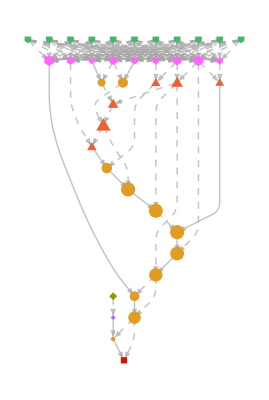

```mathematica
proofBoolean["ProofGraphWeighted"]
```

```mathematica
proofBoolean[]
```

```mathematica
(*Prove that the set of points of discontinuity of a monotonic function is finite or denumerable


*)
```